# Measure meeting angles & test generalized Gibbs–Thomson relation in the 3-species mutual inhibition system

Import Comsol simulation of a triple interface junction on a circular domain in the 3-species McRD system with mutual inhibition.

## Setup

### Load format specifiers to import Comsol data

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->Automatic
];
```

### Functions for fitting junctions

The interfaces are determined based on the squared norm of the gradient of the total-density fields B (m2+c2) & C (m3+c3).
These gradient fields are evaluated in Comsol and exported on a square grid.
We fit the interfaces by a combination of an arc (for the AB / AC interfaces) with constant curvature and a straight line for the BC interface (due to symmetry of the chosen parameters).
Fitting is done by determining the minimal distance of each point of the square grid to the interface line (arc + straight line; function “pointLoss” below). The loss function is defined as the sum over these distances squared weighted by the value of the squared norm of the gradient. The sum is performed for both the gradients of field B and C and runs in each case over all points on the grid for which the squared norm of the gradient is at least half the maximum value (function “lossCircleLine”). This latter condition excludes weak gradients occuring outside the fitted interface regions.
To account for the offset between the maxima of the gradients of field B and C in the BC interface, a shift dInt is included in the fitting.
To find the minimum of the loss function the Mathematica function FindMinimum is used (function “fitCircleLine”).

```mathematica
ClearAll@pointLoss;
pointLoss[pnt_,x0_,R_,phiInt_,phiLin_]:=Block[{
xint=x0+R{Cos[phiInt],Sin[phiInt]},
eLin={Cos[phiLin],Sin[phiLin]},
eLinN={-Sin[phiLin],Cos[phiLin]},
ePhi={-Sin[phiInt],Cos[phiInt]}*Sign[{Cos[phiLin],Sin[phiLin]}.{-Sin[phiInt],Cos[phiInt]}],
dx,dxLin,dxPhi
},
dx=pnt[[;;2]]-xint;
dxLin=dx.eLin;
dxPhi=dx.ePhi;
pnt[[3]]*
If[dxPhi>=0,
If[dxLin>=0,
(dx.eLinN)^2,
Norm[dx]^2
],
If[dxLin>=0,
Min[{(dx.eLinN)^2,(R-Norm[pnt[[;;2]]-x0])^2}],
(R-Norm[pnt[[;;2]]-x0])^2
]
]
];
```

```mathematica
ClearAll@lossCircleLine;
lossCircleLine[dataSelB_,dataSelC_,xJunc_?VectorQ,dInt_?NumericQ,R_?NumericQ,phiCircleB_?NumericQ,phiLin_?NumericQ]:=Block[{
lossB,
lossC,
x0,(*circle center*)
phiInt,(*angular direction from circle center to intersection point of circle (AB/AC interface) and line (BC interface)*)
eLinN={-Sin[phiLin],Cos[phiLin]}} (*normal vector of the BC interface (pointing in the direction at angle Pi/2+phiLin)*),
x0=xJunc+dInt*eLinN+R{Cos[phiCircleB],Sin[phiCircleB]};
phiInt=phiCircleB-Pi;
lossB=Mean[pointLoss[#,x0,R,phiInt,phiLin]&/@dataSelB];
x0=xJunc+ReflectionMatrix[eLinN].(dInt*eLinN+R{Cos[phiCircleB],Sin[phiCircleB]});
phiInt=-phiCircleB+2phiLin+Pi;
lossC=Mean[pointLoss[#,x0,R,phiInt,phiLin]&/@dataSelC];
lossB+lossC
];
```

```mathematica
ClearAll@fitCircleLine;
fitCircleLine[dataB_,dataC_,grid_,iniCond_]:=Block[{
xyDataB,
linDataB,
xyDataC,
linDataC,
max,
dataSelB,
dataSelC,
xJunc,(*coord. of junction point*)
x,(*x-coord. of junction*)
y,(*y-coord. of junction*)
dInt,(*normal offset from junction point of BC interface measured by B or C grad. *)
R,(*curvature radius of AB and AC interfaces*)
phiCircleB,(*angular direction from intersection point of circle and line to center of circle*)
phiLin,(*angular direction of line (BC interface)*)
fitRes
},
xyDataB=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataB},{3,1,2}];
linDataB=Flatten[xyDataB,1];
max=Max@linDataB[[All,3]];
dataSelB=Select[linDataB,#[[3]]>max/2&]; (*get rid of near-zero values*)

xyDataC=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataC},{3,1,2}];
linDataC=Flatten[xyDataC,1];
max=Max@linDataC[[All,3]];
dataSelC=Select[linDataC,#[[3]]>max/2&];

fitRes=Last@FindMinimum[
lossCircleLine[dataSelB,dataSelC,{x,y},dInt,100R,phiCircleB,phiLin],
{
{x,First[xJunc/.iniCond],Min[grid[[1]]],Max[grid[[1]]]},
{y,Last[xJunc/.iniCond],Min[grid[[1]]],Max[grid[[1]]]},
{dInt,dInt/.iniCond,0,10},
{R,R/100/.iniCond,10^-2,10^2},
{phiCircleB,phiCircleB/.iniCond,0,2Pi},
{phiLin,phiLin/.iniCond,-Pi,Pi}
},AccuracyGoal->5,PrecisionGoal->5];

{
xJunc->({x,y}/.fitRes),
dInt->(dInt/.fitRes),
R->(100R/.fitRes),
phiCircleB->(phiCircleB/.fitRes),
phiLin->(phiLin/.fitRes)
}
];
```

### Functions for measuring the effective interfacial tensions

The effective interfacial tensions are calculated far from the junction from the cross section of the single interfaces.

```mathematica
ClearAll@evalPoints;(*adapt to the geometry of the interfaces (tangent vector of AC interface points towards/away from the junction if center of fitted circle lies right/left of interface)*)
evalPoints[angles_,domainRadius_]:=Quiet[{
{
(xJunc/.angles[[3]])+(domainRadius-xJunc[[1]])/2{Cos[phiLin],Sin[phiLin]},
{Cos[phiLin],Sin[phiLin]}
},
{
(xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB-(domainRadius+xJunc[[1]])/2/R],Sin[phiCircleB-(domainRadius+xJunc[[1]])/2/R]},
{-Sin[phiCircleB-(domainRadius+xJunc[[1]])/2/R],Cos[phiCircleB-(domainRadius+xJunc[[1]])/2/R]}
},
{
(xJunc/.angles[[3]])-dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[-phiCircleB+2phiLin],Sin[-phiCircleB+2phiLin]}-R{Cos[-phiCircleB+2phiLin+(domainRadius+xJunc[[1]])/2/R],Sin[-phiCircleB+2phiLin+(domainRadius+xJunc[[1]])/2/R]},
{-Sin[-phiCircleB+2phiLin+(domainRadius+xJunc[[1]])/2/R],Cos[-phiCircleB+2phiLin+(domainRadius+xJunc[[1]])/2/R]}
}
}/.angles[[3]]];
```

```mathematica
ClearAll@measureσ;
measureσ[angles_,dataσ_,grid_]:=Block[{
measurementPoints,
tvecBC,
nvecBC,
tvecAC,
nvecAC,
tvecAB,
nvecAB,
xyData,
dataAC,
dataAB,
dataBC,
σABAC,
σBC,
BCDomainCorners,
boundaryDist,
junctionDist,
dx=Abs[grid[[1,2,1]]-grid[[1,1,1]]],
L=Max[grid[[1,All,1]]]+Abs[grid[[1,2,1]]-grid[[1,1,1]]]/2
},
(*determine geometry of rectangles to measure σ*)
measurementPoints=evalPoints[angles,L];
tvecBC=measurementPoints[[1,2]];
nvecBC={-#[[2]],#[[1]]}&@measurementPoints[[1,2]];
tvecAC=measurementPoints[[2,2]];
nvecAC={#[[2]],-#[[1]]}&@measurementPoints[[2,2]];
tvecAB=measurementPoints[[3,2]];
nvecAB={#[[2]],-#[[1]]}&@measurementPoints[[3,2]];

xyData=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataσ},{3,1,2}];
dataAC={nvecAC.(#[[{1,2}]]-measurementPoints[[2,1]]),#[[3]]}&/@Select[Flatten[xyData[[Floor[Length[xyData]/2];;]](*These restrictions to certain parts of the data are to make the selection faster. Needs to be changed depending on where the junction is positioned within the data.*),1],((Abs[tvecAC.(#[[{1,2}]]-measurementPoints[[2,1]])]<2)&&(Abs[nvecAC.(#[[{1,2}]]-measurementPoints[[2,1]])]<1.5))&];

dataAB={nvecAB.(#[[{1,2}]]-measurementPoints[[3,1]]),#[[3]]}&/@Select[Flatten[xyData[[;;Floor[Length[xyData]/2]]],1],((Abs[tvecAB.(#[[{1,2}]]-measurementPoints[[3,1]])]<2)&&(Abs[nvecAB.(#[[{1,2}]]-measurementPoints[[3,1]])]<1.5))&];
(*determine σAB=σAC as average of the both measurements*)
σABAC=(Total[dataAC[[All,2]]]+Total[dataAB[[All,2]]])*dx^2/8;

BCDomainCorners={#+1.5nvecBC,#-1.5nvecBC}&@measurementPoints[[1,1]]+2tvecBC;
boundaryDist=dist/.FindRoot[Max[Norm/@(BCDomainCorners+dist tvecBC)]==L,{dist,0}];
(*ensure that the edge of the measurement region is at least 1 distant from the junction*)
junctionDist=Norm[measurementPoints[[1,1]]-(xJunc/.angles[[3]])]-2;
If[junctionDist>1,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],((Abs[tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<2)&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/4;,
If[boundaryDist>0,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],(((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))<2)&&((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))>-(2+junctionDist-1))&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/(4+junctionDist-1);,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],(((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))<(2+boundaryDist))&&((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))>-(2+junctionDist-1))&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
σBC=Total[dataBC[[All,2]]]*dx^2/(4+junctionDist-1+boundaryDist);
]
];

Print[
ListPlot[{dataAC,dataBC},PlotRange->All]
];
{σABAC,σBC}
];
```

### Functions for measuring the core turnover

To calculate the core turnover, one first calculates the triangular area around the junction core in which the core turnover is calculated.
To this end, the function evalPointsCT uses the junction positions and interface directions fitted above. Assuming the specific layout of the interfaces, it calculates the intersection points of the triangle edges with the interfaces and the tangent vectors of the interfaces at these points.
The function measureCT calculates the core turnover from the modified core turnover by evaluating its integral over the triangular region.

```mathematica
ClearAll@evalPointsCT;
evalPointsCT[angles_,domainRadius_]:=Quiet[{
{
(xJunc/.angles[[3]])+(domainRadius-xJunc[[1]])0.8{Cos[phiLin],Sin[phiLin]},
{Cos[phiLin],Sin[phiLin]}
},
{
(xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB-5/R],Sin[phiCircleB-5/R]},
{-Sin[phiCircleB-5/R],Cos[phiCircleB-5/R]}
},
{
(xJunc/.angles[[3]])-dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[-phiCircleB+2phiLin],Sin[-phiCircleB+2phiLin]}-R{Cos[-phiCircleB+2phiLin+5/R],Sin[-phiCircleB+2phiLin+5/R]},
{-Sin[-phiCircleB+2phiLin+5/R],Cos[-phiCircleB+2phiLin+5/R]}
}
}/.angles[[3]]];
```

```mathematica
ClearAll@measureCT;(*adapt signs of tangent vectors in the triangleTests to the geometry of the interfaces*)
measureCT[angles_,{dataCTx_,dataCTy_},gridCT_]:=Block[{
measurementPoints,
tvecBC,
tvecAC,
tvecAB,
xyData,
triangleTests,
coreData,
dataAC,
dataAB,
dataBC,
σABAC,
σBC,
dx=Abs[gridCT[[1,2,1]]-gridCT[[1,1,1]]],
L=Max[gridCT[[1,All,1]]]
},
(*determine geometry of rectangles to measure core turnover*)
measurementPoints=evalPointsCT[angles,L];
tvecBC=measurementPoints[[1,2]];
tvecAC=measurementPoints[[2,2]];
tvecAB=measurementPoints[[3,2]];

xyData=Flatten[Transpose[{gridCT[[All,All,1]],gridCT[[All,All,2]],dataCTx,dataCTy},{3,1,2}],1];
triangleTests=Function[x,And@@((#[[1]].(x-#[[2]])<0)&/@Transpose[{{tvecBC,tvecAC,-tvecAB},measurementPoints[[All,1]]}])];
coreData=Select[xyData,triangleTests[#[[{1,2}]]]&];

{angles[[1]],2{Total[coreData[[All,3]]],
Total[coreData[[All,4]]]}*dx^2}
];
```

### Functions to determine the correction to the core turnover due to interface curvature

The integral of the modified core turnover is calculated far from the junction core over sections of the isolated, curved interfaces. If the interfaces were straight, the integral would vanish. Due to the curvature, it gives a finite contribution which must be subtracted from the integral over the triangular core region determined above.
As the modified core turnover is a vector, the contributions due to interface curvature determined at a distance from the junction must be rotated back by the amount the interface tangent direction changed between the junction position and the evaluation regions. These rotated curvature contributions calculated with measureCTCorr are then subtracted from the integral determined in function measureCT.

```mathematica
ClearAll@evalPointsCTCorr;(*adapt measArclength to the evalPointsCT chosen above to calculate the core turnover & sign of ang to the geometry of the interfaces*)
Options[evalPointsCTCorr]={"measArclength"->5};
evalPointsCTCorr[angles_,{leftMeasurementEdge_,upperMeasurementEdge_},opts:OptionsPattern[]]:=Quiet[
Block[
{arc=OptionValue["measArclength"],ang1=ang/.FindRoot[First[((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB-ang],Sin[phiCircleB-ang]})/.angles[[3]]]==leftMeasurementEdge,{ang,10/R/.angles[[3]]}],
ang2=ang/.FindRoot[Last[((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB-ang],Sin[phiCircleB-ang]})/.angles[[3]]]==upperMeasurementEdge,{ang,10/R/.angles[[3]]}],
ang
},
ang=Min[ang1,ang2];
{
{
((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB-ang],Sin[phiCircleB-ang]}),
{-Sin[phiCircleB-ang],Cos[phiCircleB-ang]}
},
{
((xJunc/.angles[[3]])+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB-ang+arc/R],Sin[phiCircleB-ang+arc/R]}),{-Sin[phiCircleB-ang+arc/R],Cos[phiCircleB-ang+arc/R]}
},
{
((xJunc/.angles[[3]])+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB-ang],Sin[phiCircleB-ang]})),
ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].{-Sin[phiCircleB-ang],Cos[phiCircleB-ang]}
},
{
((xJunc/.angles[[3]])+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}-R{Cos[phiCircleB-ang+arc/R],Sin[phiCircleB-ang+arc/R]})),ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].{-Sin[phiCircleB-ang+arc/R],Cos[phiCircleB-ang+arc/R]}
},
ang
}/.angles[[3]]]];
```

```mathematica
ClearAll@measureCTCorr;(*adapt measArclength & rotation matrices to the evalPointsCT chosen above to calculate the core turnover& sign of domainTests to geometry of interfaces*)
Options[measureCTCorr]={"halfStretch"->False,"measurementWidth"->1.5};
measureCTCorr[angles_,{dataCTx_,dataCTy_},gridCT_,opts:OptionsPattern[]]:=Block[{
measurementPoints,
tvecAC1,
tvecAC2,
nvecAC1,
nvecAC2,
tvecAB1,
tvecAB2,
nvecAB1,
nvecAB2,
ang,
xyData,
domainTests,
corrData,
ACcorr,
ABcorr,
corr,
dx=Abs[gridCT[[1,2,1]]-gridCT[[1,1,1]]],
leftMeasurementEdge=Min[gridCT[[1,All,1]]]+1,
upperMeasurementEdge=Max[gridCT[[All,1,2]]]-1
},
(*determine geometry of rectangles to measure σ*)
measurementPoints=evalPointsCTCorr[angles,{leftMeasurementEdge,upperMeasurementEdge},"measArclength"->If[OptionValue["halfStretch"],2,4]];
tvecAC1=measurementPoints[[1,2]];
nvecAC1={#[[2]],-#[[1]]}&@measurementPoints[[1,2]];
tvecAC2=measurementPoints[[2,2]];
nvecAC2={#[[2]],-#[[1]]}&@measurementPoints[[2,2]];
tvecAB1=measurementPoints[[3,2]];
nvecAB1={#[[2]],-#[[1]]}&@measurementPoints[[3,2]];
tvecAB2=measurementPoints[[4,2]];
nvecAB2={#[[2]],-#[[1]]}&@measurementPoints[[4,2]];
ang=measurementPoints[[-1]];

xyData=Flatten[Transpose[{gridCT[[All,All,1]],gridCT[[All,All,2]],dataCTx,dataCTy},{3,1,2}],1];
domainTests=Function[x,(tvecAC1.(x-measurementPoints[[1,1]])<0&&tvecAC2.(x-measurementPoints[[2,1]])>0&&(Abs[nvecAC1.(x-measurementPoints[[1,1]])]<OptionValue["measurementWidth"]))];
corrData=Select[xyData,domainTests[#[[{1,2}]]]&];
ACcorr=(2{Total[corrData[[All,3]]],
Total[corrData[[All,4]]]}*dx^2);

domainTests=Function[x,(tvecAB1.(x-measurementPoints[[3,1]])<0&&tvecAB2.(x-measurementPoints[[4,1]])>0&&(Abs[nvecAB1.(x-measurementPoints[[3,1]])]<OptionValue["measurementWidth"]))];
corrData=Select[xyData,domainTests[#[[{1,2}]]]&];
ABcorr=(2{Total[corrData[[All,3]]],
Total[corrData[[All,4]]]}*dx^2);

corr=(RotationMatrix[ang-5/R/.angles[[3]]]+If[OptionValue["halfStretch"],RotationMatrix[ang-2.5/R/.angles[[3]]],0]).ACcorr
+
(RotationMatrix[-(ang-5/R/.angles[[3]])]+If[OptionValue["halfStretch"],RotationMatrix[-(ang-2.5/R/.angles[[3]])],0]).ABcorr;

{
angles[[1]],
corr
}
];
```

## Simulation on domain of radius 15

## Import data - mutual inhibition system Tuning strength of inhibition

Prepare exported Comsol data beforehand by: sed -i.bu ‘s/NaN/0/g’ <filename.txt>

Interfaces will be determined from the finite squared norm of the gradients of the total-density fields

```mathematica
dataGrad=Import[NotebookDirectory[]<>"mutuallySuppressedAttachment-Dc_1-NeumannAngles-interfaces-fine.txt","Comsol2DSweep"];
```

```mathematica
dataGradB=dataGrad["((m2x+c2x)^2+(m2y+c2y)^2)"];
```

```mathematica
dataGradC=dataGrad["((m3x+c3x)^2+(m3y+c3y)^2)"];
```

```mathematica
grid=dataGrad["Grid"];
```

Import the field that, integrated across the respective interface, gives the effective interfacial tensions

```mathematica
dataST=Import[NotebookDirectory[]<>"mutuallySuppressedAttachment-Dc_1-NeumannAngles-surfaceTension-fine.txt","Comsol2DSweep"];
```

```mathematica
dataσ=dataST["Dm1*((m1x+c1x)^2+(m1y+c1y)^2)+Dm2*((m2x+c2x)^2+(m2y+c2y)^2)+Dm3*((m3x+c3x)^2+(m3y+c3y)^2)"];
```

Import fields that are integrated to determine the core contribution T_core

```mathematica
dataCT=Import[NotebookDirectory[]<>"mutuallySuppressedAttachment-Dc_1-NeumannAngles-coreTurnover-fine.txt","Comsol2DSweep"];
```

```mathematica
dataCoreTurnoverX=dataCT["(1-Dm1/Dc)*(m1x+c1x)*f1+(1-Dm2/Dc)*(m2x+c2x)*f2+(1-Dm3/Dc)*(m3x+c3x)*f3"];
dataCoreTurnoverY=dataCT["(1-Dm1/Dc)*(m1y+c1y)*f1+(1-Dm2/Dc)*(m2y+c2y)*f2+(1-Dm3/Dc)*(m3y+c3y)*f3"];
```

```mathematica
gridCT=dataCT["Grid"];
```

## Example density plot

```mathematica
exampleDensities=Import[NotebookDirectory[]<>"mutuallySuppressedAttachment-Dc_1-NeumannAngles-membraneDensities-kRatio_199_5-fine.txt","Comsol2DSweep"];
```

```mathematica
dataA=exampleDensities["m1"];
dataB=exampleDensities["m2"];
dataC=exampleDensities["m3"];
```

```mathematica
plotProfile=With[{
norm=If[#==0,1,#]&/@(Flatten@dataA[[1]]+Flatten@dataB[[1]]+Flatten@dataC[[1]]),
white=If[#==0,{255,255,255},{0,0,0}]&/@(Flatten@dataA[[1]]+Flatten@dataB[[1]]+Flatten@dataC[[1]])
},
Show[
ImageRotate[Image[Partition[(({192,207,240}*#)&/@(Flatten@dataA[[1]]/norm))+(({255,215,207}*#)&/@(Flatten@dataB[[1]]/norm))+(({255,228,179}*#)&/@(Flatten@dataC[[1]]/norm))+
white,Length[dataA[[1]]]]/255,ImageSize->400],-Pi/2]
]
]
```

-Graphics-

## Fit interface lines, i.e., the meeting angles at the interface junction

```mathematica
iniCond={xJunc->{0,0},dInt->0.1,R->750.,phiCircleB->Pi/4,phiLin->0.};
```

```mathematica
angleList=Block[{fit=0,fitOld,phiCircleB,phiLin},
Table[
Print[dataGrad["SweepValues"][[1,i]]];
fitOld=fit;
fit=fitCircleLine[dataGradB[[i]],dataGradC[[i]],grid,If[i==1,iniCond,Join[{R->Min[100,(R/.fitOld)]},DeleteCases[fitOld,R->_]]]];
(*Show fit result*)
Print[Show[
ListDensityPlot[Flatten[Transpose[{grid[[;;;;10,;;;;10,1]],grid[[;;;;10,;;;;10,2]],dataGradB[[Floor@i,;;;;10,;;;;10]]+dataGradC[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],PlotRange->All,InterpolationOrder->0,AspectRatio->1],
Graphics[{Black,
Circle[((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}),R,{Pi,Pi+phiCircleB}],
Darker@Red,
Line[{((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}),((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}+500{Cos[phiLin],Sin[phiLin]})}],
Black,
Circle[((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]})),R,{Pi-phiCircleB+2phiLin,Pi}],
Darker@Red,
Line[{((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]})),((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+500{Cos[phiLin],Sin[phiLin]}))}]}/.fit]
]];

{
dataGrad["SweepValues"][[1,i]],
2Pi-2(phiCircleB-phiLin+Pi/2/.fit),
fit
},
{i,Range[1,18](*for higher values, the simulation domain is too small; simulations with larger domains analyzed further below*)}]
];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

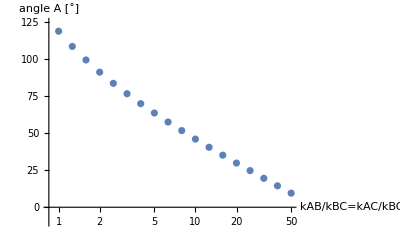

```mathematica
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{-10,125},AxesLabel->{"kAB/kBC=kAC/kBC", "angle A [˚]"}]
```

#### fitList

```mathematica
(*angleList={{1,2.0782906099130862,{xJunc->{0.14571929517086155,0.00033726338797944905},dInt->0.19667781493194658,R->1114.9629264210228,phiCircleB->0.5340981871348109,phiLin->0.0024471652964572796}},{1.2589,1.898545089256908,{xJunc->{0.9401550488506193,0.004769053671633157},dInt->0.18372805299832018,R->147.55985498781783,phiCircleB->0.6267613415023685,phiLin->0.00523755933592611}},{1.5849,1.738594158328791,{xJunc->{1.6542120836275673,0.006912617954107379},dInt->0.1783001294127265,R->86.56812153846882,phiCircleB->0.7056237088703619,phiLin->0.0041244612398607435}},{1.9953,1.5948707302541774,{xJunc->{2.3111809424879697,0.002106385948706001},dInt->0.17760030631514379,R->65.07125257403455,phiCircleB->0.7743710629033308,phiLin->0.0010101012355227341}},{2.5119,1.4627011437302713,{xJunc->{2.9264558777840444,0.01184511900683517},dInt->0.17994106074759178,R->53.891157615203724,phiCircleB->0.8434347668599823,phiLin->0.003989011930221576}},{3.1623,1.3401252674839057,{xJunc->{3.5173179976273246,0.001946620641280829},dInt->0.1835311615708714,R->47.29807610165299,phiCircleB->0.9012055862232559,phiLin->0.00047189317031218604}},{3.9811,1.2228778409691845,{xJunc->{4.097204818392222,0.08259439888635446},dInt->0.18889972146143932,R->42.76761117921126,phiCircleB->0.9794843837316556,phiLin->0.0201269774213515}},{5.0119,1.1123961766380095,{xJunc->{4.6671711756087095,0.05193771566429582},dInt->0.1957425131266384,R->39.60848647853964,phiCircleB->1.0256901792551052,phiLin->0.011091940779213093}},{6.3096,1.0058246759187295,{xJunc->{5.246723302185297,0.017589044646132233},dInt->0.2036886489395775,R->37.349281445910606,phiCircleB->1.0712223604538293,phiLin->0.0033383716182972065}},{7.9433,0.9047792684005707,{xJunc->{5.828569189062608,0.0601389206588386},dInt->0.21319848596559696,R->35.72688707927355,phiCircleB->1.1287156639107603,phiLin->0.010308971316149107}},{10,0.8046267453664866,{xJunc->{6.440121136034926,0.03092267881214702},dInt->0.2240021366664604,R->34.46379316079527,phiCircleB->1.1732495138519994,phiLin->0.0047665597403462245}},{12.589,0.7078584975251898,{xJunc->{7.075803065370163,0.012157648560193886},dInt->0.23565833390402124,R->33.54399754077387,phiCircleB->1.2185853164053615,phiLin->0.0017182383730598295}},{15.849,0.6144493310397863,{xJunc->{7.738106934019962,-0.019382375078084716},dInt->0.24915346432643112,R->32.891946788294455,phiCircleB->1.2610492552653905,phiLin->-0.002522406009613015}},{19.953,0.5214841761271023,{xJunc->{8.453592045311533,0.03089180800126517},dInt->0.2649774589659904,R->32.442824324215806,phiCircleB->1.3136976664034252,phiLin->0.003643427672079884}},{25.119,0.4323446236283939,{xJunc->{9.200847016945264,0.008976089145451482},dInt->0.28365445847672766,R->32.167549800221686,phiCircleB->1.3555788086196614,phiLin->0.000954793638961655}},{31.623,0.34128975196994915,{xJunc->{10.040403418714211,0.13410905041616059},dInt->0.30464119634309744,R->32.00886353871134,phiCircleB->1.4134941460507082,phiLin->0.013342695240786486}},{39.811,0.2527288444735909,{xJunc->{10.949363940122437,0.06883878543961845},dInt->0.33003909843468004,R->32.0153971843516,phiCircleB->1.4506806366601506,phiLin->0.006248732102049392}},{50.119,0.1666310784626459,{xJunc->{11.93605735455842,0.3046252644884269},dInt->0.3642555801084074,R->32.219881799048764,phiCircleB->1.5129681501790249,phiLin->0.025487362615451346}}};*)
```

## Determine effective interfacial tensions σAB, σAC, σBC

Find points on the interfaces that are distant from the junction to measure the effective interfacial tensions.
Around this point, σ is determined by integrating the field dataσ over a rectangle crossing the interface. This integral is then divided by the width of the rectangle.

```mathematica
evalPointsS=evalPoints[#,15]&/@angleList;
```

Show the interface segments used to calculate σ

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{grid[[;;;;10,;;;;10,1]],grid[[;;;;10,;;;;10,2]],dataσ[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1
],
Graphics[
Join[{Darker@Red,Thick},Flatten[{
Line[{{#[[1,1]],#[[1,2]]}-2#[[2]],{#[[1,1]],#[[1,2]]}+2#[[2]]}],
Line[{{#[[1,1]],#[[1,2]]}+2#[[2]]-1.5{-#[[2,2]],#[[2,1]]},{#[[1,1]],#[[1,2]]}+2#[[2]]+1.5{-#[[2,2]],#[[2,1]]}}],Line[{{#[[1,1]],#[[1,2]]}-2#[[2]]-1.5{-#[[2,2]],#[[2,1]]},{#[[1,1]],#[[1,2]]}-2#[[2]]+1.5{-#[[2,2]],#[[2,1]]}}]
}&/@evalPointsS[[Floor@i]],1]]
]
]
,{i,1,Length@angleList}]
```

```mathematica
σList=Table[
{angleList[[k,1]],
measureσ[angleList[[k]],dataσ[[k]],grid]
},{k,Length@angleList}];
```

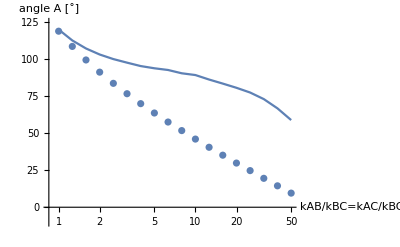

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{-10,125},AxesLabel->{"kAB/kBC=kAC/kBC", "angle A [˚]"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList
},
Joined->True]
]
```

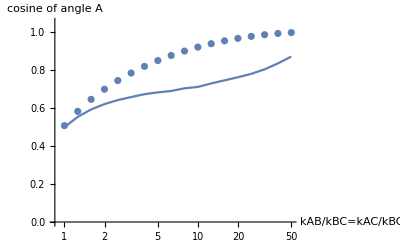

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1.05},AxesLabel->{"kAB/kBC=kAC/kBC", "cosine of angle A"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList
},
Joined->True]
]
```

#### σList

```mathematica
(*σList={{1,{0.028895250804294177,0.02880786645047465}},{1.2589,{0.03093590554470078,0.03423501832992573}},{1.5849,{0.03280473932914697,0.03884832689682682}},{1.9953,{0.03450326662240944,0.04281076213524504}},{2.5119,{0.036059785352357245,0.04625581188440602}},{3.1623,{0.03747547913709505,0.04927203395103724}},{3.9811,{0.038753475733367834,0.05212126959647072}},{5.0119,{0.03996177254530109,0.054513480516828756}},{6.3096,{0.04110181846420656,0.05667055175327141}},{7.9433,{0.04200111053928215,0.059084613856767054}},{10,{0.04292678006314106,0.061019108879449176}},{12.589,{0.043757513878268435,0.06381147224386556}},{15.849,{0.04452265803282223,0.06636359903176613}},{19.953,{0.04523939821557125,0.06890831620594288}},{25.119,{0.045899895648558085,0.07155134465217447}},{31.623,{0.04650275166244741,0.07469516807715838}},{39.811,{0.04703774591478973,0.07850528260407828}},{50.119,{0.04757886772505086,0.0828389175652818}}};*)
```

## Core contribution T_core

To determine the x and y components of T_core, we need to integrate the field dataCoreTurnoverX & dataCoreTurnoverY over a triangle whose sides are perpendicular to the three interfaces.
If all interfaces are straight, the triangle can be arbitrarily large because the integrals over a single interface (far from the core region) vanishes.
As two interfaces are curved here, this is not the case and we need to substract the contribution that stems from the interfaces being curved (coreTurnoverCorr).

```mathematica
evalPointsCTS=evalPointsCT[#,15]&/@angleList;
```

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridCT[[;;;;100,;;;;100,1]],gridCT[[;;;;100,;;;;100,2]],dataCoreTurnoverX[[Floor@i,;;;;100,;;;;100]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1/2],
Graphics[Join[
{Darker@Red,Thick},
Circle[#[[1]],0.1]&/@evalPointsCTS[[Floor@i]],
Line[{#[[1]],#[[1]]+1#[[2]]}]&/@evalPointsCTS[[Floor@i]]]]
]
,{i,1,Length@angleList}]
```

```mathematica
coreTurnover={};
Monitor[Do[
Block[{ct},
ct=measureCT[angleList[[k]],{dataCoreTurnoverX[[k]],dataCoreTurnoverY[[k]]},gridCT];
Print[ct];
AppendTo[coreTurnover,ct];
],{k,Length@angleList}];,k]
```

{1,{0.000155425,-0.0000427457}}

{1.2589,{0.000294196,0.0000408493}}

{1.5849,{-0.000180555,-0.000157497}}

{1.9953,{-0.00113808,0.0000367365}}

{2.5119,{-0.00242897,-0.000133744}}

{3.1623,{-0.00396233,8.68172×10^-6}}

{3.9811,{-0.00565536,0.0000163009}}

{5.0119,{-0.00731585,-0.00022117}}

{6.3096,{-0.00903208,-0.000208902}}

{7.9433,{-0.0106548,0.000187798}}

{10,{-0.0119699,0.000159288}}

{12.589,{-0.0130854,-0.00015918}}

{15.849,{-0.0139419,0.0000434923}}

{19.953,{-0.014319,-0.000235271}}

{25.119,{-0.0141927,-0.000210856}}

{31.623,{-0.0134433,-0.0000899688}}

{39.811,{-0.0119135,0.00037256}}

{50.119,{-0.0093614,0.000153881}}

Angle prediction without correcting for interface curvature:

```mathematica
junctionAnglesPred=Table[
Block[{
thetaAB0=phiCircleB/.angleList[[k,3]],
thetaAC0=-phiCircleB+2phiLin/.angleList[[k,3]],
thetaBC=phiLin/.angleList[[k,3]]
},
{angleList[[k,1]],
{θAC,thetaBC,θAB}/.FindRoot[({Cos[thetaBC],Sin[thetaBC]}σList[[k,2,2]])
+({Cos[θAB],Sin[θAB]}σList[[k,2,1]])
+({Cos[θAC],Sin[θAC]}σList[[k,2,1]])
==coreTurnover[[k,2]],{{θAB,thetaAB0,0,Pi+thetaBC},{θAC,thetaAC0,-Pi+thetaBC,0}}]
}],{k,Length@angleList}]
```

{{1,{-2.0856,0.00244717,2.09351}},{1.2589,{-2.14736,0.00523756,2.15552}},{1.5849,{-2.19977,0.00412446,2.21605}},{1.9953,{-2.26109,0.0010101,2.26139}},{2.5119,{-2.30531,0.00398901,2.31839}},{3.1623,{-2.36038,0.000471893,2.36093}},{3.9811,{-2.39409,0.020127,2.42984}},{5.0119,{-2.44199,0.0110919,2.46871}},{6.3096,{-2.49083,0.00333837,2.50295}},{7.9433,{-2.5442,0.010309,2.55628}},{10,{-2.58527,0.00476656,2.58887}},{12.589,{-2.64038,0.00171824,2.64737}},{15.849,{-2.69746,-0.00252241,2.6922}},{19.953,{-2.73269,0.00364343,2.74437}},{25.119,{-2.7731,0.000954794,2.77961}},{31.623,{-2.80432,0.0133427,2.82898}},{39.811,{-2.8605,0.00624873,2.86311}},{50.119,{-2.87014,0.0254874,2.9126}}}

```mathematica
angleAPred={#[[1]],(Min[Join[#,{360-Total@#}]]&@(180/Pi*Differences[#[[2]]]))}&/@junctionAnglesPred
```

{{1,119.636},{1.2589,113.463},{1.5849,106.992},{1.9953,100.881},{2.5119,95.0815},{3.1623,89.4885},{3.9811,83.6095},{5.0119,78.6375},{6.3096,73.8777},{7.9433,67.7641},{10,63.5439},{12.589,57.0342},{15.849,51.1953},{19.953,46.1874},{25.119,41.8534},{31.623,37.2353},{39.811,32.061},{50.119,28.6738}}

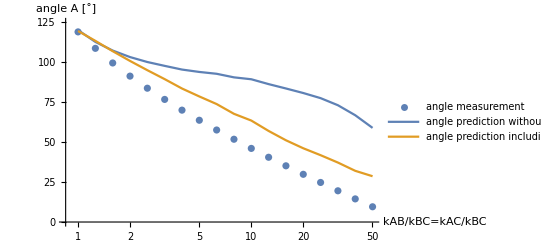

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{0,125},PlotLegends->{"angle measurement"},AxesLabel->{"kAB/kBC=kAC/kBC", "angle A [˚]"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
angleAPred
},
Joined->True,
PlotLegends->{"angle prediction without core contribution","angle prediction including core contribution (without curvature correction)"}]
]
```

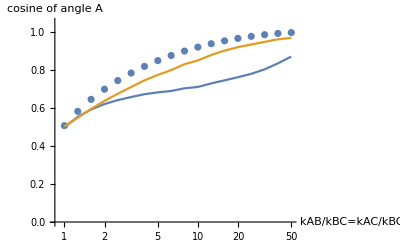

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1.05},AxesLabel->{"kAB/kBC=kAC/kBC", "cosine of angle A"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
{#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPred
},
Joined->True]
]
```

#### Core turnover list

```mathematica
(*coreTurnover={{1,{0.0001554252963052382,-0.000042745704129354634}},{1.2589,{0.000294196476474936,0.00004084925188653695}},{1.5849,{-0.00018055506574467383,-0.00015749735888220367}},{1.9953,{-0.0011380801361532374,0.000036736475108044285}},{2.5119,{-0.002428973313067978,-0.00013374394044112135}},{3.1623,{-0.003962326684170775,8.68172148866469*^-6}},{3.9811,{-0.005655362678297311,0.00001630086562108703}},{5.0119,{-0.007315850453027102,-0.00022117004061418777}},{6.3096,{-0.00903207852215801,-0.00020890208294294116}},{7.9433,{-0.010654821249374112,0.0001877983902480002}},{10,{-0.011969925489699808,0.00015928797336240907}},{12.589,{-0.013085395714954415,-0.00015918042035186093}},{15.849,{-0.013941886440512885,0.00004349229822505364}},{19.953,{-0.014318953726316738,-0.0002352709087234316}},{25.119,{-0.014192728426812132,-0.0002108560717179581}},{31.623,{-0.013443310621379139,-0.00008996878720845033}},{39.811,{-0.011913529486225777,0.00037255959104412115}},{50.119,{-0.009361401161348572,0.000153881185858784}}};*)
```

### Correction to core turnover due to curved interfaces

Calculate turnover integral over the curved interface at a distance from the junction, rotate the turnover vector such that that interface piece alines with its contribution in the core-turnover integral and substrate this correction vector from the above calculated turnover vector.

```mathematica
evalPointsCTCorrS=Table[
evalPointsCTCorr[junction,{-4,4},"measArclength"->5],
{junction,angleList}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridCT[[;;;;50,;;;;50,1]],gridCT[[;;;;50,;;;;50,2]],dataCoreTurnoverX[[Floor@i,;;;;50,;;;;50]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1/2],
Graphics[Join[
{Darker@Red,Thick},
Circle[#[[1]],0.1]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]],#[[1]]+1#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]]-1.5 {-#[[2,2]],#[[2,1]]},#[[1]]+1.5 {-#[[2,2]],#[[2,1]]}}]&/@evalPointsCTCorrS[[Floor@i,;;-2]],
Line[{#[[1]]-1.5{-#[[2,2]],#[[2,1]]},#[[1]]-1.5 {-#[[2,2]],#[[2,1]]}-5#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,{1,3}]],
Line[{#[[1]]+1.5{-#[[2,2]],#[[2,1]]},#[[1]]+1.5{-#[[2,2]],#[[2,1]]}-5#[[2]]}]&/@evalPointsCTCorrS[[Floor@i,{1,3}]]
]]
]
,{i,1,Length@angleList}]
```

For the first 1-9 parameters, we need to determine the correction term on a smaller stretch of the interface as the interfaces are too short to measure the full stretch at a certain distance away from the junction.

```mathematica
coreTurnoverCorr={};
Monitor[Do[
Block[{
corr
},
corr=measureCTCorr[angleList[[k]],{dataCoreTurnoverX[[k]],dataCoreTurnoverY[[k]]},gridCT,"halfStretch"->If[k<10,True,False]];
Print[corr];
AppendTo[coreTurnoverCorr,corr];
],{k,1,Length@angleList}];,k]
```

{1,{-0.000205544,0.0000157047}}

{1.2589,{0.00112865,-6.32854×10^-6}}

{1.5849,{0.00213725,-0.0000273667}}

{1.9953,{0.00302149,3.04811×10^-6}}

{2.5119,{0.00365134,0.0000102661}}

{3.1623,{0.00400846,-0.000147159}}

{3.9811,{0.00437144,2.9042×10^-6}}

{5.0119,{0.00458475,0.0000684716}}

{6.3096,{0.00470088,-0.0000167087}}

{7.9433,{0.00468275,0.0000375428}}

{10,{0.00459319,0.000129421}}

{12.589,{0.00439794,0.0000647079}}

{15.849,{0.00415778,0.0000850715}}

{19.953,{0.00380802,0.000100901}}

{25.119,{0.00344429,0.0000502414}}

{31.623,{0.00301962,0.0000110936}}

{39.811,{0.00252515,0.0000416175}}

{50.119,{0.0020364,0.0000724729}}

```mathematica
junctionAnglesPredCorr=Table[
Block[{
thetaAB0=phiCircleB/.angleList[[k,3]],
thetaAC0=-phiCircleB+2phiLin/.angleList[[k,3]],
thetaBC=phiLin/.angleList[[k,3]]
},
{angleList[[k,1]],
{θAC,thetaBC,θAB}/.FindRoot[({Cos[thetaBC],Sin[thetaBC]}σList[[k,2,2]])
+({Cos[θAB],Sin[θAB]}σList[[k,2,1]])
+({Cos[θAC],Sin[θAC]}σList[[k,2,1]])
==coreTurnover[[k,2]]-coreTurnoverCorr[[k,2]],{{θAB,thetaAB0,0,Pi+thetaBC},{θAC,thetaAC0,-Pi+thetaBC,0}}]
}],{k,Length@angleList}]
```

{{1,{-2.08093,0.00244717,2.09}},{1.2589,{-2.16965,0.00523756,2.17719}},{1.5849,{-2.24202,0.00412446,2.25613}},{1.9953,{-2.31926,0.0010101,2.31967}},{2.5119,{-2.37656,0.00398901,2.38912}},{3.1623,{-2.4422,0.000471893,2.43757}},{3.9811,{-2.48446,0.020127,2.51779}},{5.0119,{-2.53824,0.0110919,2.56517}},{6.3096,{-2.59375,0.00333837,2.60459}},{7.9433,{-2.65314,0.010309,2.66547}},{10,{-2.69566,0.00476656,2.70239}},{12.589,{-2.75821,0.00171824,2.76641}},{15.849,{-2.82088,-0.00252241,2.8179}},{19.953,{-2.85813,0.00364343,2.87162}},{25.119,{-2.89883,0.000954794,2.90622}},{31.623,{-2.9299,0.0133427,2.95399}},{39.811,{-2.98452,0.00624873,2.98796}},{50.119,{-2.98043,0.0254874,3.02351}}}

```mathematica
angleAPredCorr={#[[1]],(Min[Join[#,{360-Total@#}]]&@(180/Pi*Differences[#[[2]]]))}&/@junctionAnglesPredCorr
```

{{1,119.369},{1.2589,110.945},{1.5849,102.275},{1.9953,94.2088},{2.5119,86.9467},{3.1623,80.4101},{3.9811,73.3927},{5.0119,67.5961},{6.3096,62.1569},{7.9433,55.2665},{10,50.7146},{12.589,43.4625},{15.849,36.9214},{19.953,31.7092},{25.119,27.3951},{31.623,22.8781},{39.811,17.802},{50.119,16.}}

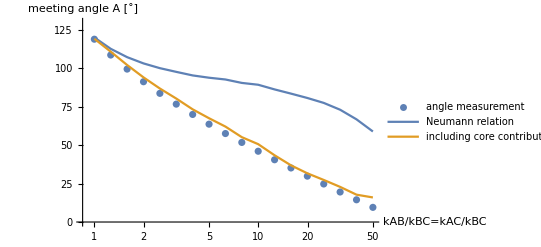

```mathematica
Show[
ListLogLinearPlot[{#[[1]],180/Pi*#[[2]]}&/@angleList,PlotRange->{0,130},AxesLabel->{"kAB/kBC=kAC/kBC","meeting angle A [˚]"},PlotLegends->{"angle measurement"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
angleAPredCorr
},
Joined->True,
PlotLegends->{"Neumann relation", "including core contribution"}]
]
```

Above, the x-Axis label is wrong.

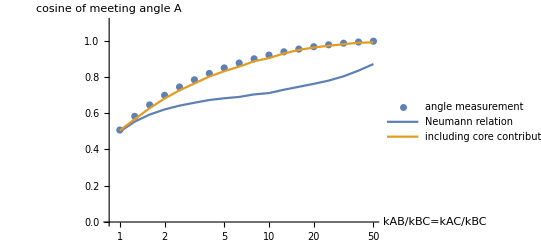

```mathematica
Show[
ListLogLinearPlot[{#[[1]],Cos[#[[2]]/2]}&/@angleList,PlotRange->{0,1.1},AxesLabel->{"kAB/kBC=kAC/kBC","cosine of meeting angle A"},PlotLegends->{"angle measurement"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
{#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPredCorr
},
Joined->True,
PlotLegends->{"Neumann relation", "including core contribution"}]
]
```

#### Correction list

```mathematica
(*coreTurnoverCorr={{1,{-0.00020554432741691899,0.000015704703645131254}},{1.2589,{0.0011286499117352806,-6.32853708302497*^-6}},{1.5849,{0.0021372542322938516,-0.000027366682690832924}},{1.9953,{0.003021493648445832,3.0481100751094704*^-6}},{2.5119,{0.003651341630309465,0.000010266068277428294}},{3.1623,{0.004008457510116524,-0.00014715926917721178}},{3.9811,{0.004371444762327371,2.904197353478799*^-6}},{5.0119,{0.004584753499872298,0.00006847163008418845}},{6.3096,{0.004700875215511885,-0.000016708695672440488}},{7.9433,{0.004682750115016006,0.000037542831346105456}},{10,{0.004593193025729473,0.0001294209215960589}},{12.589,{0.004397939792802393,0.00006470785165935133}},{15.849,{0.004157783686288063,0.0000850715189200258}},{19.953,{0.003808020950214997,0.00010090076487068254}},{25.119,{0.0034442899093433043,0.00005024139534646078}},{31.623,{0.0030196207316769016,0.000011093579196332602}},{39.811,{0.002525145160800008,0.00004161754788828149}},{50.119,{0.0020363956532878326,0.00007247286584818532}}};*)
```

## Simulation on an enlarged domain of radius 30 to reliably determine lower meeting angles

## Import data - mutually suppressed attachment Tuning rate constant of suppression

Prepare exported Comsol data beforehand by: sed -i.bu ‘s/NaN/0/g’ <filename.txt> etc.

Interfaces will be determined from the finite squared norm of the gradients of the total-density fields

```mathematica
dataGradL=Import[NotebookDirectory[]<>"mutuallySuppressedAttachment-Dc_1-NeumannAngles-L_30-squareGradients.txt","Comsol2DSweep"];
```

```mathematica
dataGradLB=dataGradL["((m2x+c2x)^2+(m2y+c2y)^2)"];
```

```mathematica
dataGradLC=dataGradL["((m3x+c3x)^2+(m3y+c3y)^2)"];
```

```mathematica
gridL=dataGradL["Grid"];
```

Import the field that, integrated across the respective interface, gives the effective interfacial tensions

```mathematica
dataSTL=Import[NotebookDirectory[]<>"mutuallySuppressedAttachment-Dc_1-NeumannAngles-L_30-surfaceTension.txt","Comsol2DSweep"];
```

```mathematica
dataσL=dataSTL["Dm1*((m1x+c1x)^2+(m1y+c1y)^2)+Dm2*((m2x+c2x)^2+(m2y+c2y)^2)+Dm3*((m3x+c3x)^2+(m3y+c3y)^2)"];
```

Import fields that are integrated to determine the core contribution T_core

```mathematica
dataCTL=Import[NotebookDirectory[]<>"mutuallySuppressedAttachment-Dc_1-NeumannAngles-L_30-coreTurnover.txt","Comsol2DSweep"];
```

```mathematica
dataCoreTurnoverLX=dataCTL["(1-Dm1/Dc)*(m1x+c1x)*f1+(1-Dm2/Dc)*(m2x+c2x)*f2+(1-Dm3/Dc)*(m3x+c3x)*f3"];
dataCoreTurnoverLY=dataCTL["(1-Dm1/Dc)*(m1y+c1y)*f1+(1-Dm2/Dc)*(m2y+c2y)*f2+(1-Dm3/Dc)*(m3y+c3y)*f3"];
```

```mathematica
gridCTL=dataCTL["Grid"];
```

## Fit interface lines

```mathematica
iniCond={xJunc->{25,0},dInt->1,R->50.,phiCircleB->Pi/2,phiLin->0.};
```

```mathematica
angleListL=Block[{fit=0,fitOld,phiCircleB,phiLin},
Table[
Print[dataGradL["SweepValues"][[1,i]]];
fitOld=fit;
fit=fitCircleLine[dataGradLB[[i]],dataGradLC[[i]],gridL,If[i==1,iniCond,Join[{R->Min[10000,(R/.fitOld)]},DeleteCases[fitOld,R->_]]]];
(*Show fit result*)
Print[Show[
ListDensityPlot[Flatten[Transpose[{gridL[[;;;;10,;;;;10,1]],gridL[[;;;;10,;;;;10,2]],dataGradLB[[Floor@i,;;;;10,;;;;10]]+dataGradLC[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],PlotRange->All,InterpolationOrder->0,AspectRatio->1],
Graphics[{Black,
Circle[((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]}),R,{Pi,Pi+phiCircleB}],
Darker@Red,
Line[{((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}),((xJunc/.fit)+dInt{-Sin[phiLin],Cos[phiLin]}+500{Cos[phiLin],Sin[phiLin]})}],
Black,
Circle[((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+R{Cos[phiCircleB],Sin[phiCircleB]})),R,{Pi-phiCircleB+2phiLin,Pi}],
Darker@Red,
Line[{((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]})),((xJunc/.fit)+ReflectionMatrix[{-Sin[phiLin],Cos[phiLin]}].(dInt{-Sin[phiLin],Cos[phiLin]}+500{Cos[phiLin],Sin[phiLin]}))}]}/.fit]
]];

{
dataGradL["SweepValues"][[1,i]],
2Pi-2(phiCircleB-phiLin+Pi/2/.fit),
fit
},
{i,1,Length@First@dataGradL["SweepValues"]}]
];
```

63.096

-Graphics-

79.433

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

100

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

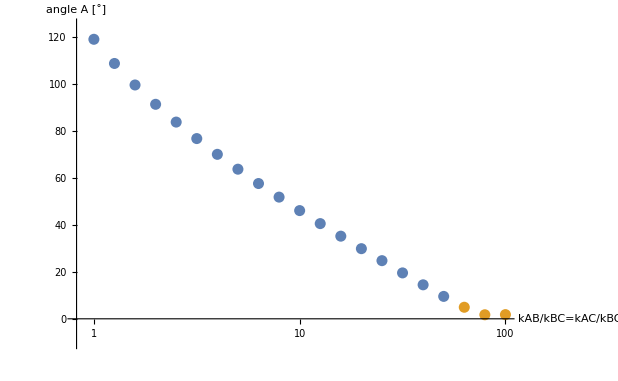

```mathematica
ListLogLinearPlot[{{#[[1]],180/Pi*#[[2]]}&/@angleList,{#[[1]],180/Pi*#[[2]]}&/@angleListL},PlotRange->{-10,125},AxesLabel->{"kAB/kBC=kAC/kBC", "angle A [˚]"}]
```

#### fitList

```mathematica
(*angleListL={{63.096,0.08586730739177462,{xJunc->{26.59578840578106,-0.37802763787231647},dInt->0.41927027862986027,R->65.58744848280413,phiCircleB->1.5136554451889639,phiLin->-0.014207227910045483}},{79.433,0.03006073744112925,{xJunc->{27.940123481505278,0.33523721954296154},dInt->0.5656310921220684,R->66.08988938205192,phiCircleB->1.567758760294012,phiLin->0.011992802219679705}},{100,0.03108432249202231,{xJunc->{27.020590332051924,0.2941848106487866},dInt->0.9263424472209064,R->66.65063162721087,phiCircleB->1.5661462355170173,phiLin->0.010892069968131954}}};*)
```

## Determine effective interfacial tensions σAB, σAC, σBC

Find points on the interfaces that are distant from the junction to measure σ.
Around this point, σ is determined by integrating the field dataσ over a rectangle crossing the interface. This integral is then divided by the width of the rectangle.

```mathematica
evalPointsL=evalPoints[#,30]&/@angleListL;
```

Show the interface segments used to calculate σ

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridL[[;;;;50,;;;;50,1]],gridL[[;;;;50,;;;;50,2]],dataσL[[Floor@i,;;;;50,;;;;50]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->1
],
Graphics[
Join[{Darker@Red,Thick},Flatten[{
Line[{{#[[1,1]],#[[1,2]]}-2#[[2]],{#[[1,1]],#[[1,2]]}+2#[[2]]}],
Line[{{#[[1,1]],#[[1,2]]}+2#[[2]]-1.5{-#[[2,2]],#[[2,1]]},{#[[1,1]],#[[1,2]]}+2#[[2]]+1.5{-#[[2,2]],#[[2,1]]}}],Line[{{#[[1,1]],#[[1,2]]}-2#[[2]]-1.5{-#[[2,2]],#[[2,1]]},{#[[1,1]],#[[1,2]]}-2#[[2]]+1.5{-#[[2,2]],#[[2,1]]}}]
}&/@evalPointsL[[Floor@i]],1]]
]
]
,{i,1,Length@angleListL}]
```

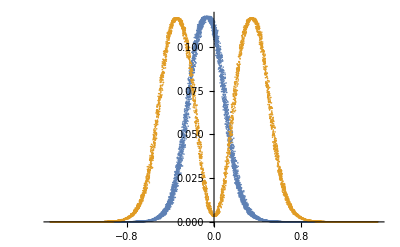

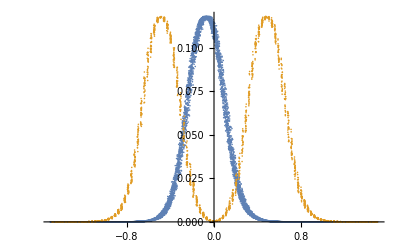

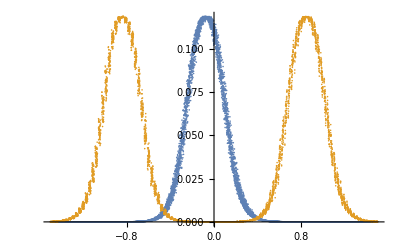

```mathematica
σListL=Table[
{angleListL[[k,1]],
measureσ[angleListL[[k]],dataσL[[k]],gridL]
},{k,Length@angleListL}];
```

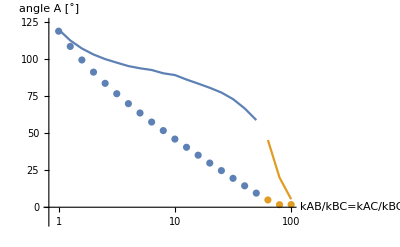

```mathematica
Show[
ListLogLinearPlot[{{#[[1]],180/Pi*#[[2]]}&/@angleList,{#[[1]],180/Pi*#[[2]]}&/@angleListL},PlotRange->{-10,125},AxesLabel->{"kAB/kBC=kAC/kBC", "angle A [˚]"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σListL
},
Joined->True]
]
```

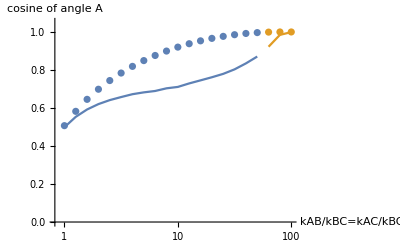

```mathematica
Show[
ListLogLinearPlot[{{#[[1]],Cos[#[[2]]/2]}&/@angleList,{#[[1]],Cos[#[[2]]/2]}&/@angleListL},PlotRange->{0,1.05},AxesLabel->{"kAB/kBC=kAC/kBC", "cosine of angle A"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σListL
},
Joined->True]
]
```

#### σList

```mathematica
(*σListL={{63.096,{0.04782346851209751,0.08820840686115904}},{79.433,{0.04821883793758114,0.09496428515546566}},{100,{0.04865141975897867,0.09719361114071488}}};*)
```

## Core contribution T_core

To determine the x and y components of T_core, we need to integrate the field dataCoreTurnoverX & dataCoreTurnoverY over a triangle whose sides are perpendicular to the three interfaces.
If all interfaces are straight, the triangle can be arbitrarily large because the integrals over a single interface (far from the core region) vanishes.
As two interfaces are curved here, this is not the case and we need to substract the contribution that stems from the interfaces being curved (coreTurnoverCorr).

```mathematica
evalPointsCTL=evalPointsCT[#,30]&/@angleListL;
```

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridCTL[[;;;;10,;;;;10,1]],gridCTL[[;;;;10,;;;;10,2]],dataCoreTurnoverLX[[Floor@i,;;;;10,;;;;10]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->6/15],
Graphics[Join[
{Darker@Red,Thick},
Circle[#[[1]],0.1]&/@evalPointsCTL[[Floor@i]],
Line[{#[[1]],#[[1]]+1#[[2]]}]&/@evalPointsCTL[[Floor@i]]]]
]
,{i,1,Length@angleListL}]
```

```mathematica
coreTurnoverL={};
Monitor[Do[
Block[{c},
ct=measureCT[angleListL[[k]],{dataCoreTurnoverLX[[k]],dataCoreTurnoverLY[[k]]},gridCTL];
Print[ct];
AppendTo[coreTurnoverL,ct];
],{k,Length@angleListL}];,k]
```

{63.096,{-0.00650138,-0.0000368942}}

{79.433,{-0.000823275,0.000164914}}

{100,{0.000425713,0.0000823076}}

Angle prediction without correcting for interface curvature:

```mathematica
junctionAnglesPredL=Table[
Block[{
thetaAB0=phiCircleB/.angleListL[[k,3]],
thetaAC0=-phiCircleB+2phiLin/.angleListL[[k,3]],
thetaBC=phiLin/.angleListL[[k,3]]
},
{angleListL[[k,1]],
{θAC+2Pi,thetaBC,θAB}/.FindRoot[({Cos[thetaBC],Sin[thetaBC]}σListL[[k,2,2]])
+({Cos[θAB],Sin[θAB]}σListL[[k,2,1]])
+({Cos[θAC],Sin[θAC]}σListL[[k,2,1]])
==coreTurnoverL[[k,2]],{{θAB,thetaAB0,0,2Pi(*Pi+thetaBC*)},{θAC,thetaAC0,-2Pi(*-Pi+thetaBC*),0}}]
}],{k,Length@angleListL}]
```

{{63.096,{3.26893,-0.0142072,2.98857}},{79.433,{3.26811,0.0119928,3.03541}},{100,{3.25667,0.0108921,3.04669}}}

```mathematica
angleAPredL={#[[1]],(Min[Join[#,{360-Total@#}]]&@(180/Pi*Differences[Sort@#[[2]]]))}&/@junctionAnglesPredL
```

{{63.096,16.0637},{79.433,13.3325},{100,12.0309}}

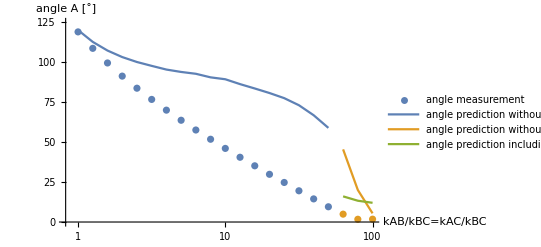

```mathematica
Show[
ListLogLinearPlot[{{#[[1]],180/Pi*#[[2]]}&/@angleList,{#[[1]],180/Pi*#[[2]]}&/@angleListL},PlotRange->{0,125},PlotLegends->{"angle measurement"},AxesLabel->{"kAB/kBC=kAC/kBC", "angle A [˚]"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σListL,
angleAPredL
},
Joined->True,
PlotLegends->{"angle prediction without core contribution",
"angle prediction without core contribution","angle prediction including core contribution (without curvature correction)"}]
]
```

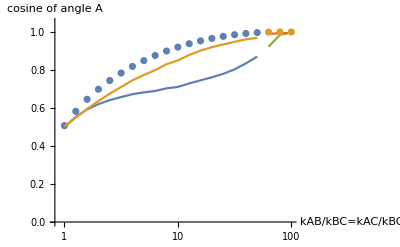

```mathematica
Show[
ListLogLinearPlot[{{#[[1]],Cos[#[[2]]/2]}&/@angleList,{#[[1]],Cos[#[[2]]/2]}&/@angleListL},PlotRange->{0,1.05},AxesLabel->{"kAB/kBC=kAC/kBC", "cosine of angle A"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
{#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPred,
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σListL,
{#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPredL
},
Joined->True]
]
```

#### Core turnover list

```mathematica
(*coreTurnoverL={{63.096,{-0.006501378753077089,-0.00003689417817223574}},{79.433,{-0.0008232750041501279,0.0001649138836962781}},{100,{0.0004257130196245264,0.00008230755818760985}}};*)
```

### Correction to core turnover due to curved interfaces

Calculate turnover integral over the curved interface at a distance from the junction, rotate the turnover vector such that that interface piece alines with its contribution in the core-turnover integral and substrate this correction vector from the above calculated turnover vector.

```mathematica
evalPointsCTCorrL=Table[
evalPointsCTCorr[junction,{16,2}],
{junction,angleListL}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[
Flatten[Transpose[{gridCTL[[;;;;50,;;;;50,1]],gridCTL[[;;;;50,;;;;50,2]],dataCoreTurnoverLX[[Floor@i,;;;;50,;;;;50]]},{3,1,2}],1],
PlotRange->All,
InterpolationOrder->0,
AspectRatio->6/15],
Graphics[Join[
{Darker@Red,Thick},
Circle[#[[1]],0.1]&/@evalPointsCTCorrL[[Floor@i,;;-2]],
Line[{#[[1]],#[[1]]+1#[[2]]}]&/@evalPointsCTCorrL[[Floor@i,;;-2]],
Line[{#[[1]]-1 {-#[[2,2]],#[[2,1]]},#[[1]]+1{-#[[2,2]],#[[2,1]]}}]&/@evalPointsCTCorrL[[Floor@i,;;-2]]
]]
]
,{i,1,Length@angleListL}]
```

```mathematica
coreTurnoverCorrL={};
Monitor[Do[
Block[{
corr
},
corr=measureCTCorr[angleListL[[k]],{dataCoreTurnoverLX[[k]],dataCoreTurnoverLY[[k]]},gridCTL,"measurementWidth"->1];
Print[corr];
AppendTo[coreTurnoverCorrL,corr];
],{k,Length@angleListL}];,k]
```

{63.096,{0.000567935,-0.0000247704}}

{79.433,{0.000351608,-0.0000239248}}

{100,{0.000369739,0.0000483474}}

```mathematica
junctionAnglesPredCorrL=Table[
Block[{
thetaAB0=phiCircleB/.angleListL[[k,3]],
thetaAC0=-phiCircleB+2phiLin/.angleListL[[k,3]],
thetaBC=phiLin/.angleListL[[k,3]]
},
{angleListL[[k,1]],
{θAC+2Pi,thetaBC,θAB}/.FindRoot[({Cos[thetaBC],Sin[thetaBC]}σListL[[k,2,2]])
+({Cos[θAB],Sin[θAB]}σListL[[k,2,1]])
+({Cos[θAC],Sin[θAC]}σListL[[k,2,1]])
==coreTurnoverL[[k,2]]-coreTurnoverCorrL[[k,2]],{{θAB,thetaAB0,0,2Pi(*Pi+thetaBC*)},{θAC,thetaAC0,-2Pi(*-Pi+thetaBC*),0}}]
}],{k,Length@angleListL}]
```

{{63.096,{3.21656,-0.0142072,3.04058}},{79.433,{3.23046,0.0119928,3.07249}},{100,{3.21049,0.0108921,3.0938}}}

```mathematica
angleAPredCorrL={#[[1]],(Min[Join[#,{360-Total@#}]]&@(180/Pi*Differences[Sort@#[[2]]]))}&/@junctionAnglesPredCorrL
```

{{63.096,10.0831},{79.433,9.05071},{100,6.68572}}

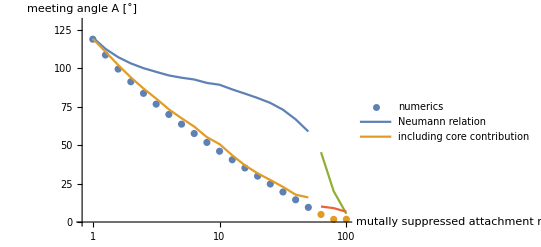

```mathematica
Show[
ListLogLinearPlot[{{#[[1]],180/Pi*#[[2]]}&/@angleList,{#[[1]],180/Pi*#[[2]]}&/@angleListL},PlotRange->{0,130},AxesLabel->{"mutally suppressed attachment rate kAC","meeting angle A [˚]"},PlotLegends->{"numerics"}],
ListLogLinearPlot[{
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σList,
(*{#[[1]],180/Pi*2(Pi-First@Differences[#[[2]]])}&/@junctionAnglesPredCorrL*)angleAPredCorr,
({#[[1]],180/Pi*2ArcCos[Min[1,#[[2,2]]/#[[2,1]]/2]]})&/@σListL,
(*{#[[1]],180/Pi*2(Pi-First@Differences[#[[2]]])}&/@junctionAnglesPredCorrL*)angleAPredCorrL
},
Joined->True,
PlotLegends->{"Neumann relation", "including core contribution"}]
]
```

Above, x-Axis is wrong. Should be kBC/kAB=kBC/kAC

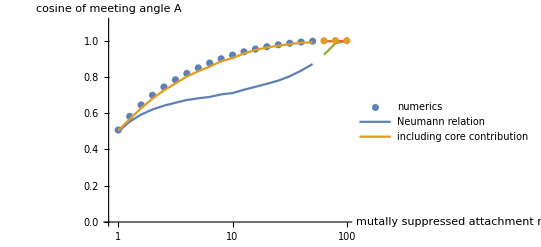

```mathematica
Show[
ListLogLinearPlot[{{#[[1]],Cos[#[[2]]/2]}&/@angleList,{#[[1]],Cos[#[[2]]/2]}&/@angleListL},PlotRange->{0,1.1},AxesLabel->{"mutally suppressed attachment rate kAC","cosine of meeting angle A"},PlotLegends->{"numerics"}],
ListLogLinearPlot[{
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σList,
(*{#[[1]],Cos[(Pi-First@Differences[#[[2]]])]}&/@junctionAnglesPredCorrL*){#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPredCorr,
({#[[1]],#[[2,2]]/#[[2,1]]/2})&/@σListL,
(*{#[[1]],Cos[(Pi-First@Differences[#[[2]]])]}&/@junctionAnglesPredCorrL*){#[[1]],Cos[Pi/180#[[2]]/2]}&/@angleAPredCorrL
},
Joined->True,
PlotLegends->{"Neumann relation", "including core contribution"}]
]
```

#### Correction list

```mathematica
(*coreTurnoverCorrL={{63.096,{0.0005679353642044805,-0.000024770431518160527}},{79.433,{0.0003516075781739438,-0.000023924808509009562}},{100,{0.0003697392925016944,0.0000483474269203049}}};*)
```